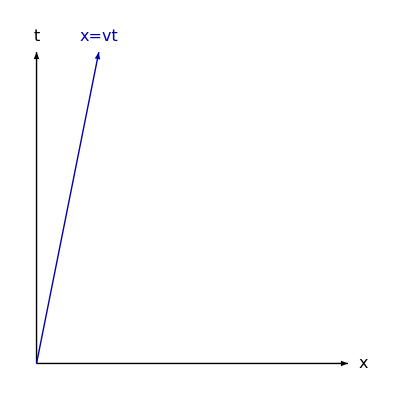

```mathematica
Str[x_,y_]:=Text[Style[x,Medium,Italic,FontSize->16,ScriptLevel->1],y];
g0={White,Rectangle[{-1/4,-1/4},{5+3/4,5+3/4}]};
g1={Black,Arrow[{{0,0},{5,0}}],Str[x,{5+1/4,0}],Arrow[{{0,0},{0,5}}],Str[t,{0,5+1/4}],Darker[Blue],Arrow[{{0,0},{1,5}}],Str["x=vt",{1,5+1/4}]};
Graphics[Join[g1]]
```

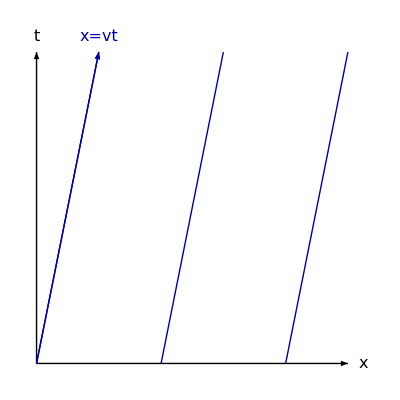

```mathematica
g2={Darker[Blue],Arrow[{{0,0},{1,5}}],AbsoluteDashing[{2Sqrt[26],2Sqrt[26]}],Line[{{2,0},{3,5}}],Dashing[None],Line[{{4,0},{5,5}}]};
Graphics[Join[g2,g1]]
```

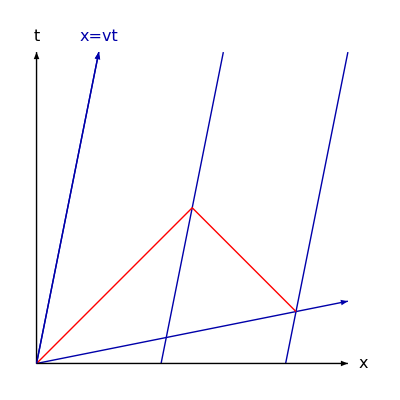

```mathematica
g3={Darker[Blue],Arrow[{{0,0},{5,1}}],Red,Line[{{0,0},{5/2,5/2},{25/6,5/6}}]};
Graphics[Join[g2,g3,g1]]
```

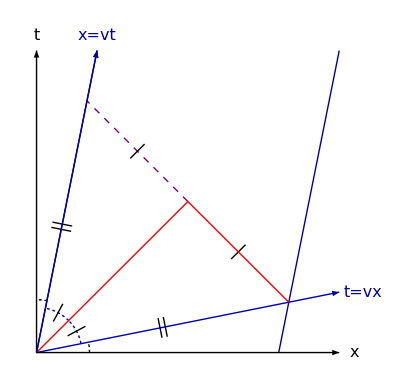

```mathematica
d={5/2,5/2};
a={Pi/4,Pi/2-Tan[1/5]};
b={Tan[1/5],Pi/4};
Hatch[x_,l_,t_]:=Rotate[Line[{x-{l,0},x+{l,0}}],t,x];
g2a={Darker[Blue],Arrow[{{0,0},{1,5}}],Line[{{4,0},{5,5}}]};
g4={Purple,Dashed,Line[{d,{5/6,25/6}}],AbsoluteDashing[{2,2}],Black,Circle[{0,0},7/8,{Pi/2-Tan[1/5],Pi/2}],Circle[{0,0},7/8,{0,Tan[1/5]}],Darker[Blue],Circle[{0,0},3/4,a],Circle[{0,0},3/4,b],EdgeForm[Purple],Opacity[0,White],Rotate[Rectangle[d,d+{1/4,1/4}],3Pi/4,d],Rotate[Rectangle[d,d+{1/4,1/4}],5Pi/4,d],Opacity[1,Black],Dashing[None],Hatch[47/48*5/12*{1,5},1/6,-Sin[1/5]],Hatch[49/48*5/12*{1,5},1/6,-Sin[1/5]],Hatch[47/48*5/12*{5,1},1/6,Pi/2+Sin[1/5]],Hatch[49/48*5/12*{5,1},1/6,Pi/2+Sin[1/5]],Hatch[d+1/2*{-5/3,5/3},1/6,Pi/4],Hatch[d+1/2*{5/3,-5/3},1/6,Pi/4],Hatch[3/4*{Cos[Mean[a]],Sin[Mean[a]]},1/6,Mean[a]],Hatch[3/4*{Cos[Mean[b]],Sin[Mean[b]]},1/6,Mean[b]],Darker[Blue],Str["t=vx",{5+2/5,1}]};
Graphics[Join[g4,g2a,g3,g1]]
```